# Powerplay

Evolutionary powerplay for Nascence materials

This example contains a search for classifiers

```mathematica
Row[{Style["Jan Koutnik, IDSIA, E-mail:  ",FontFamily->"Roman",FontSize->16],DynamicModule[{r="@"->".",bt,b=Button[bt,b=Hyperlink["mailto:"~~StringReplace[bt,{r,Reverse@r}]]]},bt="hkou.idsia@ch";Dynamic@b]}]
```

Jan Koutnik, IDSIA, E-mail:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/koutnij/git/NASCENCE/alg/mathematica/powerplay

```mathematica
LaunchKernels[2]
```

{KernelObject[1,local],KernelObject[2,local]}

## Imports

```mathematica
Import["../libMLP/bp.m"]
```

```mathematica
Import["../libNES/nes10.m"]
```

```mathematica
Import["../libCoSyNE/libCosyne9.m"]
```

```mathematica
Import["../vm/vmWrapper1.m"]
```

## VM

### In Mathematica

Vitual material is a simple MLP here :

```mathematica
nInputs=20;
```

```mathematica
actF=Tanh;
```

```mathematica
vm=randomNet[{nInputs,500,1}];
```

```mathematica
evalVM[vm_,x_]:=Last@fwdPass[vm,x]
```

```mathematica
res=Sort@Flatten[evalVM[vm,#]&/@RandomReal[{-1,1},{5,nInputs}]];
Min@res
Max@res
```

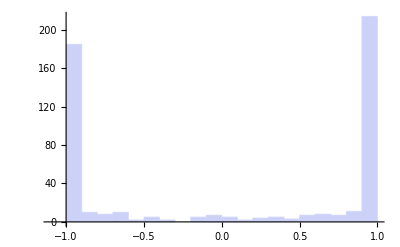

```mathematica
Histogram[res,20]
```

```mathematica
evalVM[vm_,config_,input_]:=evalVM[vm,Join[config,input]]
```

```mathematica
plotBounds[vm_,config_,set_]:=With[{points=(First/@#)&/@SortBy[GatherBy[set,Last],#⟦1,2,1⟧&]},Show[{
ContourPlot[Sign@First@evalVM[vm,config,{x,y}],{x,-1,1},{y,-1,1},Contours->{0},ContourShading->{LightRed,LightGreen},ContourStyle->Directive[Black,Dashed],FrameTicks->False,ImageSize->100],
ListPlot[points,PlotStyle->{Darker@Red,Darker@Green}]
}]]
```

### Nascence API VM

```mathematica
vmHost="localhost";
vmPort=9090;
```

```mathematica
vmPath="git/NASCENCE/vm";
```

```mathematica
vmClient=vmConnect[vmHost,vmPort,vmPath]
```

«JavaObject[nascence.vm.io.MathClient]»

```mathematica
vmClient@programmeVarElmanRandom[20,1000,20,3.0, 0.5, False, False]
```

This function evaluates the VM via Nascence API :

```mathematica
evalVMN[vmClient_,config_,input_]:=First[vmClient@evaluateArray[{Join[config,input]},255,Range[0,nPins-2]]]
```

```mathematica
AbsoluteTiming@evalVMN[vmClient,RandomReal[{-1,1},17],RandomReal[{-1,1},2]]
```

{0.00771,{1.}}

```mathematica
evalVM=evalVMN
```

evalVMN

```mathematica
vm=vmClient
```

«JavaObject[nascence.vm.io.MathClient]»

```mathematica
res=Sort@Flatten[MapThread[evalVM[vm,#1,#2]&,{RandomReal[{-1,1},{100,dim}],RandomReal[{-1,1},{100,2}]}]];
Min@res
Max@res
```

-1.

1.

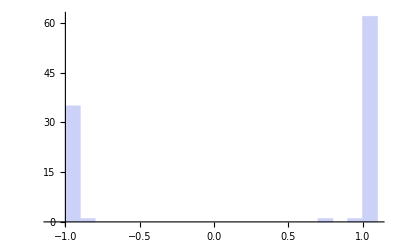

```mathematica
Histogram[res,20]
```

## Powerplay Experiment, 2-space Classifiers

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/koutnij/git/NASCENCE/alg/mathematica/powerplay

In this example a space of classifiers is explored.

```mathematica
maxTasks=1000;
```

```mathematica
SeedRandom[30];
taskSet=RandomReal[{-1,1},{maxTasks,2}];
```

```mathematica
fitFn[g_,set_]:=With[{diff=Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)-set⟦All,2⟧]},Total[diff^2]]
```

This adds a number of non - solved tasks :

```mathematica
fitFn[g_,set_]:=With[{eval=Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)]},Mean[(eval-Flatten@set⟦All,2⟧)^2]+Length[set]-Count[MapThread[Equal,{Sign@eval,Flatten@set⟦All,2⟧}],True]]
```

```mathematica
fitFn[g_]:=fitFn[g,trainingSet]
```

```mathematica
solvesAllTasksQ[g_,set_]:=Equal[Sign@Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)],Flatten@set⟦All,2⟧]
```

```mathematica
solvesAllTasksQ[g_]:=solvesAllTasksQ[g,trainingSet]
```

```mathematica
optimize[pop_,fitFn_,trainingSet_,nGen_]:=Module[{popTmp},NestWhile[(popTmp=coSyNEstep[#,fitFn[#,trainingSet]&,minimize->True,mutate->0.8,permuteAll->True,verbose->False,elite->1];Print[{popTmp⟦1,1⟧,solvesAllTasksQ[popTmp⟦1,2⟧,trainingSet]}];popTmp)&,pop,Not[solvesAllTasksQ[#⟦1,2⟧,trainingSet]]&,1,
nGen]]
```

```mathematica
reevaluate[pop_,fitFn_]:=SortBy[{fitFn[#],#}&/@pop⟦All,2⟧,First]
```

```mathematica
appendTask[set_,config_]:=With[{point=taskSet⟦Length[set]+1⟧},Append[set,{point,-Sign[evalVM[vm,config,point]]}]]
```

```mathematica
powerplay[fitFn_,popSize_,nGen_,nTasks_]:=Module[{pop,set},
set={{taskSet⟦1⟧,{1}}};(*first task*)
pop=SortBy[newRandomPop[popSize,dim,NormalDistribution[0,1],fitFn[#,set]&],First];
Print["Generated population"];
Nest[
(Print["# of tasks : "<>ToString@Length[set]];
pop=optimize[pop,fitFn,set,nGen];(*optimize*)
Print@plotBounds[vm,pop⟦1,2⟧,set];
set=appendTask[set,pop⟦1,2⟧];(*add next task*)
pop=reevaluate[pop,fitFn[#,set]&];
pop)&
,pop,nTasks]
]
```

### Experiment

Powerplay with population size of 8, 30 generations of CoSyNE and 10 consecutive classification tasks to solve :

```mathematica
nPins=20;nOutputs=1;nInputs=nPins-nOutputs;dim=nInputs-2;
```

```mathematica
popSize=20;
```

```mathematica
fitFn[RandomReal[{-1,1},17],set]
```

2.

```mathematica
pop=powerplay[fitFn,32,300,10];
```

Generated population

# of tasks : 1

-Graphics-

# of tasks : 2

{3.,False}

{0.000768935,True}

-Graphics-

# of tasks : 3

{2.33333,False}

{2.33333,False}

{2.33333,False}

«7 more identical outputs»

{0.00100474,True}

-Graphics-

# of tasks : 4

{0.0553633,True}

-Graphics-

# of tasks : 5

-Graphics-

# of tasks : 6

{1.43508,False}

{1.43508,False}

{0.0000922722,True}

-Graphics-

# of tasks : 7

{0.00211128,True}

-Graphics-

# of tasks : 8

{1.46886,False}

{1.46886,False}

{1.46886,False}

«17 more identical outputs»

{1.42285,False}

{1.42285,False}

{1.42285,False}

«13 more identical outputs»

$Aborted